```mathematica
Quit[];
```

```mathematica
(*Stavenga et al 1993*)
(*Vitamin A1 rhodopsin constants*)
a0α=380;
a1α=6.09;
a0β=247;
a1β=3.59;
Aα=1;
Aβ=0.29;

(*Peak Absorabance Wavelengths*)
λmaxα=500; (*μm*)
λmaxβ=350; (*μm*)
(*μm*)
```

```mathematica
xα[λ_]:= Log[λ/λmaxα];
xβ[λ_]:= Log[λ/λmaxβ];
(*SSH template calculations*)
α[λ_]:= Aα*Exp[-a0α*xα[λ]^2*(1+a1α*xα[λ]+(3/8)*a1α^2*(xα[λ])^2)];
β[λ_]:= Aβ*Exp[-a0β*xβ[λ]^2*(1+a1β*xβ[λ]+(3/8)*a1β^2*(xβ[λ])^2)];
A[λ_]:= α[λ]+β[λ];
```

InterpolatingFunction[{{0.401, 0.9245}}, <>]

InterpolatingFunction::dmval: Input value {0.400006} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

Import::nffil: File not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

-Graphics-

InterpolatingFunction[{{0.322, 0.9662}}, <>]

InterpolatingFunction[{{0.322, 0.9662}}, <>]

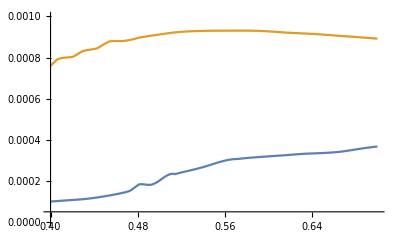

```mathematica
(*Bowker et al 1985*)
λDaylight=Import[FileNameJoin[{NotebookDirectory[],"daylightRadiance.csv"}]];
IλDaylight=Interpolation[λDaylight]
Plot[IλDaylight[x],{x,0.4,0.7},PlotRange->{{0.4,0.7},{0,10}}]
λVegetative=Import[FileNameJoin[{NotebookDirectory[],"vegetativeRadiance.csv"}]];
IλVegetative=Interpolation[λVegetative];
Plot[IλVegetative[x],{x,0.4,0.7}]
(*Lythgoe 1979*)
λStarlight=Import[FileNameJoin[{NotebookDirectory[],"starlightRadiance.csv"}]];
IλStarlight=Interpolation[λStarlight]
λMoonlight=Import[FileNameJoin[{NotebookDirectory[],"moonlightRadiance.csv"}]];
IλMoonlight=Interpolation[λMoonlight]
Plot[{IλStarlight[x],IλMoonlight[x]},{x,0.4,0.7},PlotRange->{{0.4,0.7},{10^-6,10^-3}}]
```

InterpolatingFunction[{{299.49, 700.37}}, <>]

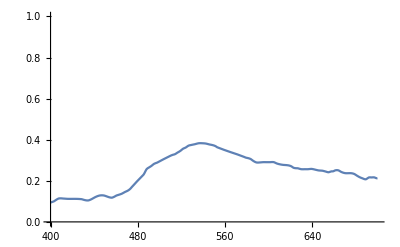

{{301.906,0.06852},{302.724,0.07984},{303.572,0.09132},{304.73,0.09674},{306.01,0.10202},{307.14,0.1045},{308.578,0.10388},{310.138,0.10218},{311.636,0.10328},{313.258,0.10342},{315.704,0.10342},{318.152,0.10372},{321.214,0.10186},{324.304,0.10154},{327.948,0.0989},{332.174,0.0955},{337.284,0.0924},{342.976,0.08868},{348.794,0.08342},{353.842,0.08094},{358.188,0.07814},{362.534,0.07566},{366.942,0.07318},{372.236,0.07132},{378.358,0.0676},{384.172,0.06512},{389.284,0.06264},{393.628,0.0614},{397.146,0.06},{400.972,0.05846},{405.164,0.05692},{409.202,0.05522},{413.304,0.05336},{417.71,0.05258},{421.626,0.05226},{425.268,0.05086},{429.368,0.05008},{434.08,0.04946},{438.976,0.04854},{444.086,0.04684},{449.654,0.04638},{455.01,0.04592},{459.66,0.0453},{464.158,0.0442},{468.166,0.04436},{471.746,0.0445},{474.986,0.0462},{477.982,0.04806},{480.582,0.04962},{483.088,0.0524},{485.38,0.05566},{488.622,0.05846},{491.956,0.06032},{495.258,0.06248},{498.562,0.06342},{502.172,0.06358},{505.17,0.06358},{508.506,0.06248},{511.962,0.06296},{515.204,0.06372},{518.446,0.0648},{521.382,0.06418},{524.928,0.06558},{529.334,0.06558},{534.964,0.06482},{541.512,0.06358},{549.038,0.06296},{556.566,0.0611},{564.154,0.05954},{571.742,0.05798},{579.268,0.05612},{586.796,0.05456},{594.384,0.05394},{601.972,0.0524},{609.498,0.05086},{616.444,0.049},{622.442,0.04746},{627.582,0.04638},{632.048,0.04576},{636.576,0.04514},{641.746,0.04546},{647.864,0.04546},{654.84,0.045},{662.49,0.045},{668.884,0.045},{674.606,0.045},{679.194,0.045},{682.65,0.045},{685.434,0.04484},{688.158,0.04514},{690.39,0.04452},{692.502,0.04482},{694.766,0.04544}}

InterpolatingFunction[{{301.906, 694.766}}, <>]

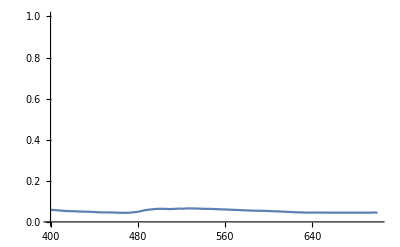

```mathematica
RRGGreen=Import[FileNameJoin[{NotebookDirectory[],"RRGGreen.csv"}]];
RRGGreenInterp=Interpolation[RRGGreen]
Plot[RRGGreenInterp[x],{x,400,700},PlotRange->{{400,700},{0,1}}]
RRGBlack=Import[FileNameJoin[{NotebookDirectory[],"RRGBlack.csv"}]];
RRGBlack=MovingAverage[RRGBlack,5]
RRGBlackInterp=Interpolation[RRGBlack]
Plot[RRGBlackInterp[x],{x,400,700},PlotRange->{{400,700},{0,1}}]
```

```mathematica
(*Warrant et al 1996*)
λ1=400; (*nm*) 
λ2=700;(*nm*) 
k=0.035; (*μm^-1*)
l=57; (*μm*) (*Bufo Bufo photoreceptor length, Warrant 1997*)
(*Subscript[E, p]=h*(c/λ)
Np=E[W/m^2]*λ[m]/(h[J/s]*c[m/s])[photons/m^2s]
h: Planck's Constant, c: speed of light
h=6.63E-34, c= 2.998E8*)
constant=10^-9/(6.63*10^-34*2.998*10^8);

QADaylight=NIntegrate[((RRGGreenInterp[λ]*IλDaylight[λ*10^-3]*λ*10^-3)*λ*constant)*(1-Exp[-k*A[λ]*l]),{λ,λ1,λ2}] (*qunta/(m^2 ssr)*)
QAStarlight=NIntegrate[(RRGGreenInterp[λ]*IλStarlight[λ*10^-3]*λ*10^-3)*λ*constant*(1-Exp[-k*A[λ]*l]),{λ,λ1,λ2}](*qunta/(m^2 ssr)*)
QAMoonlight=NIntegrate[(RRGGreenInterp[λ]*IλMoonlight[λ*10^-3]*λ*10^-3)*(λ*constant)*(1-Exp[-k*A[λ]*l]),{λ,λ1,λ2}](*qunta/(m^2 ssr)*)
```

9.97575×10^19

3.66665×10^15

1.60507×10^16

```mathematica
(*refBarley={{0.36,0.055},{0.38,0.063},{0.4,0.07},{0.42,0.077},{0.44,0.099},{0.46,0.124},{0.48,0.133},{0.5,0.156},{0.52,0.191},{0.54,0.25},{0.56,0.268},{0.58,0.264},{0.6,0.237},{0.62,0.236},{0.64,0.222},{0.66,0.212},{0.68,0.212},{0.7,0.232},{0.72,0.266},{0.74,0.304},{0.76,0.333},{0.78,0.336},{0.8,0.323}};
Rλ=Interpolation[refBarley]*)
```

InterpolatingFunction[{{0.36, 0.8}}, <>]

```mathematica
QAReflectedDaylight=NIntegrate[((RRGBlackInterp[λ]*IλDaylight[λ*10^-3]*λ*10^-3)*λ*constant)*(1-Exp[-k*A[λ]*l]),{λ,λ1,λ2}]
QAReflectedStarlight=NIntegrate[(RRGBlackInterp[λ]*IλStarlight[λ*10^-3]*λ*10^-3)*λ*constant*(1-Exp[-k*A[λ]*l]),{λ,λ1,λ2}]
QAReflectedMoonlight=NIntegrate[(RRGBlackInterp[λ]*IλMoonlight[λ*10^-3]*λ*10^-3)*(λ*constant)*(1-Exp[-k*A[λ]*l]),{λ,λ1,λ2}]
```

2.20721×10^19

7.78113×10^14

3.51591×10^15